```mathematica
θ={3,9};
P={3,1};
NUM = 2;


J=Subsets[Range[NUM],{1,NUM}];

φ[n_,t_,j_]:=Sum[θ[[i]]+t*P[[i]]-(n-t),{i,j}]-Sum[Sum[(1- KroneckerDelta[i,k])* Min[ P[[i]] , P[[k]] ],{i,j}],{k,j}];

ρ[n_,t_]:=Max[0,Max[Map[φ[n,t,#]&,J]]];
u[n_,t_]:=ρ[n+1,t-0.5]-ρ[n,t-0.5]-ρ[n+2,t+0.5]+ρ[n+1,t+0.5];
Table[IntegerPart[u[n,2]],{n,30}]
```

{0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
3
```

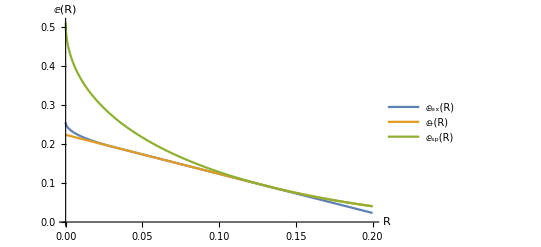

```mathematica
Subscript[E, o][ρ_]:=-Log[ 2*( 0.5 *0.9^(1/(1+ρ))+ 0.5*0.1^(1/(1+ρ)))^(1+ρ)];
Subscript[E, x][ρ_]:=-ρ Log[0.5+0.5(0.6)^(1/ρ)];
Subscript[E, ex][R_]:=MaxValue[{Subscript[E, x][ρ]-ρ R,1≤ρ},ρ];
Subscript[E, r][R_]:=MaxValue[{Subscript[E, o][ρ]-ρ R,0≤ρ≤1},ρ];
Subscript[E, sp][R_]:=MaxValue[{Subscript[E, o][ρ]-ρ R,0<ρ},ρ];
Plot[{Subscript[E, ex][R],Subscript[E, r][R],Subscript[E, sp][R]},{R,0,0.2},PlotLegends->"Expressions",AxesLabel->{R,E[R]}]
```